{{Computational basis states,Probabilities},{0,0.122},{1,0.085},{10,0.049},{11,0.098},{100,0.073},{101,0.732},{110,0.134},{111,2.222},{1000,2.075},{1001,0.305},{1010,2.014},{1011,3.772},{1100,0.5},{1101,3.833},{1110,6.348},{1111,77.637}}

{0.00122,0.00085,0.00049,0.00098,0.00073,0.00732,0.00134,0.02222,0.02075,0.00305,0.02014,0.03772,0.005,0.03833,0.06348,0.77637}

{{Computational basis states,Probabilities},{0,0},{1,0},{10,0},{11,0},{100,0},{101,0},{110,0},{111,0},{1000,0},{1001,0},{1010,0},{1011,0},{1100,0},{1101,0},{1110,0},{1111,100}}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

{{Computational basis states,Probabilities},{0,0.293},{1,1.465},{10,3.65},{11,1.489},{100,5.383},{101,0.403},{110,84.631},{111,1.489},{1000,0.061},{1001,0.037},{1010,0.024},{1011,0.024},{1100,0.928},{1101,0.037},{1110,0.085},{1111,0}}

{0.00293,0.01465,0.0365,0.01489,0.05383,0.00403,0.84631,0.01489,0.00061,0.00037,0.00024,0.00024,0.00928,0.00037,0.00085,0}

{{Computational basis states,Probabilities},{0,0},{1,0},{10,0},{11,0},{100,0},{101,0},{110,100},{111,0},{1000,0},{1001,0},{1010,0},{1011,0},{1100,0},{1101,0},{1110,0},{1111,0}}

{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}

{{Computational basis states,Probabilities},{0,4.785},{1,0.146},{10,87.39},{11,1.318},{100,0.488},{101,1.66},{110,1.636},{111,1.233},{1000,0.94},{1001,0},{1010,0.269},{1011,0},{1100,0.012},{1101,0.037},{1110,0.024},{1111,0.061}}

{0.04785,0.00146,0.8739,0.01318,0.00488,0.0166,0.01636,0.01233,0.0094,0,0.00269,0,0.00012,0.00037,0.00024,0.00061}

{{Computational basis states,Probabilities},{0,0},{1,0},{10,100},{11,0},{100,0},{101,0},{110,0},{111,0},{1000,0},{1001,0},{1010,0},{1011,0},{1100,0},{1101,0},{1110,0},{1111,0}}

{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}

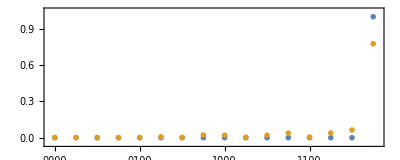

Curve1.png

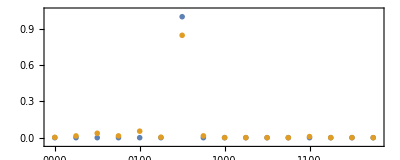

Curve2.png

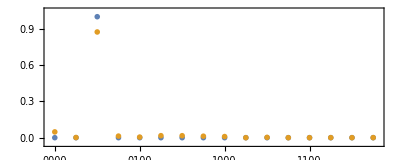

Curve3.png

```mathematica
SetDirectory[NotebookDirectory[]];

ImportDataExp=Import["Fig3(i)real.csv","CSV"]
xDataExp=Drop[ImportDataExp,1][[All,1]];
xDataExp=IntegerString[xDataExp,10,4];
yData1Exp=Drop[ImportDataExp,1][[All,2]]/100

(*xDataExp

Table[{i,Reverse[IntegerDigits[xDataExp[[i]]]]},{i,1,Length[xDataExp]}]*)
(*Reverse*)

ImportDataTheory=Import["Fig3(i)sim.csv","CSV"]
yData1Theory=Drop[ImportDataTheory,1][[All,2]]/100

ImportDataExp=Import["Fig3(ii)real.csv","CSV"]
yData2Exp=Drop[ImportDataExp,1][[All,2]]/100

ImportDataTheory=Import["Fig3(ii)sim.csv","CSV"]
yData2Theory=Drop[ImportDataTheory,1][[All,2]]/100

ImportDataExp=Import["Fig3(iii)real.csv","CSV"]
yData3Exp=Drop[ImportDataExp,1][[All,2]]/100

ImportDataTheory=Import["Fig3(iii)sim.csv","CSV"]
yData3Theory=Drop[ImportDataTheory,1][[All,2]]/100

PlotData1Exp=Table[{i,yData1Exp[[i]]},{i,1,Length[xDataExp]}];
PlotData2Exp=Table[{i,yData2Exp[[i]]},{i,1,Length[xDataExp]}];
PlotData3Exp=Table[{i,yData3Exp[[i]]},{i,1,Length[xDataExp]}];

PlotData1Theory=Table[{i,yData1Theory[[i]]},{i,1,Length[xDataExp]}];
PlotData2Theory=Table[{i,yData2Theory[[i]]},{i,1,Length[xDataExp]}];
PlotData3Theory=Table[{i,yData3Theory[[i]]},{i,1,Length[xDataExp]}];

xTicks=Table[{i,Rotate[xDataExp[[i]],Pi/2]},{i,1,Length[xDataExp]}];

PlotRangeX1=1-0.2;
PlotRangeX2=Length[xDataExp]+0.2;
PlotRangeY1=0-0.05;
PlotRangeY2=1+0.05;

DataPSize=0.05;
AspRatio=2/5;

ExportPlot=ListPlot[{PlotData1Theory,PlotData1Exp}
(*,Epilog->Text[Style["Θ=π/4",FontSize->13],Scaled[{.5,.9}]]*)
,PlotStyle->{PointSize[DataPSize],PointSize[DataPSize]},Joined->False
,PlotStyle->{
{RGBColor["#F3901A"]},
{RGBColor["#7C64A9"]}}
,Frame->True
,FrameTicks->{{All,All},{xTicks,None}}
,PlotRange->{{PlotRangeX1,PlotRangeX2},{PlotRangeY1,PlotRangeY2}}
,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman",FontSize->15]
,AspectRatio->AspRatio
(*,FrameLabel->{{"Detection probability",None},{"Hamming distance",None}}*)
,PlotMarkers->{"OpenMarkers", Large}
]
Export["Curve1.png",ExportPlot,ImageResolution->300,Background->None]
(*Export["Curve1.eps",ExportPlot,Background->None,"EmbeddedFonts"->True]*)

ExportPlot=ListPlot[{PlotData2Theory,PlotData2Exp}
(*,Epilog->Text[Style["Θ=π/2",FontSize->13],Scaled[{.5,.9}]]*)
,PlotStyle->{PointSize[DataPSize],PointSize[DataPSize]},Joined->False
,PlotStyle->{
{RGBColor["#F3901A"]},
{RGBColor["#7C64A9"]}}
,Frame->True
,FrameTicks->{{All,All},{xTicks,None}}
,PlotRange->{{PlotRangeX1,PlotRangeX2},{PlotRangeY1,PlotRangeY2}}
,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman",FontSize->15]
,AspectRatio->AspRatio
(*,FrameLabel->{{"Detection probability",None},{"Hamming distance",None}}*)
,PlotMarkers->{"OpenMarkers", Large}
]
Export["Curve2.png",ExportPlot,ImageResolution->300,Background->None]
(*Export["Curve2.eps",ExportPlot,Background->None,"EmbeddedFonts"->True]*)

ExportPlot=ListPlot[{PlotData3Theory,PlotData3Exp}
(*,Epilog->Text[Style["Θ=3π/4",FontSize->13],Scaled[{.5,.9}]]*)
,PlotStyle->{PointSize[DataPSize],PointSize[DataPSize]},Joined->False
,PlotStyle->{
{RGBColor["#F3901A"]},
{RGBColor["#7C64A9"]}}
,Frame->True
,FrameTicks->{{All,All},{xTicks,None}}
,PlotRange->{{PlotRangeX1,PlotRangeX2},{PlotRangeY1,PlotRangeY2}}
,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman",FontSize->15]
,AspectRatio->AspRatio
(*,FrameLabel->{{"Detection probability",None},{"Hamming distance",None}}*)
,PlotMarkers->{"OpenMarkers", Large}
]
Export["Curve3.png",ExportPlot,ImageResolution->300,Background->None]
(*Export["Curve3.eps",ExportPlot,Background->None,"EmbeddedFonts"->True]*)

Quit[];
```